# News Feed Creator

## Abstract

When trying to build a news aggregator, I had a problem of finding the category names of news articles, since different websites are using different tags for their content. So it is very difficult to find them on the webpage and align them. For solving this problem, I’m building a classifier that will automatically recognize the category of a news article.

## Getting Lists of URLs

```mathematica
URLlist={"http://theweek.com/section/opinion","http://theweek.com/section/feature","http://theweek.com/speedreads","http://theweek.com/5things","http://theweek.com/mostpopular","http://theweek.com/authors","http://theweek.com/section/opinion","http://theweek.com/section/feature","http://theweek.com/speedreads","http://theweek.com/5things","http://theweek.com/mostpopular","http://theweek.com/section/world","http://theweek.com/section/U.S.","http://theweek.com/section/politics","http://theweek.com/section/business","http://theweek.com/section/tech","http://theweek.com/section/science","http://theweek.com/section/entertainment","http://theweek.com/section/books","http://theweek.com/section/lifestyle","http://theweek.com/captured","http://theweek.com/audio","http://theweek.com/video","http://theweek.com/cartoons","http://theweek.com/puzzles","http://theweek.com/newsletters","http://theweek.com/covergallery","http://theweek.com/section/shopping","http://theweek.com/section/world","http://theweek.com/section/U.S.","http://theweek.com/section/politics","http://theweek.com/section/business","http://theweek.com/section/tech","http://theweek.com/section/science","http://theweek.com/section/entertainment","http://theweek.com/section/books","http://theweek.com/section/lifestyle","http://theweek.com/captured","http://theweek.com/audio","http://theweek.com/video","http://theweek.com/cartoons","http://theweek.com/puzzles","http://theweek.com/newsletters","http://theweek.com/covergallery","http://theweek.com/authors","http://theweek.com/section/shopping","http://theweek.com/section/summerreading","http://theweek.com/section/RioOlympics","http://theweek.com/section//","https://subscribe.theweek.com/servlet/Show?WESPAGE=pm/Pages/load_order.jsp&WESACTIVESESSION=TRUE&PAGE_ID=WKALL43015&MAGCODE=WK&MSCCMPLX=601WKSA01","https://subscribe.theweek.com/wes/servlet/Show?WESPAGE=csp/wk/dgord/Gift_Order.jsp&MSRSMAG=WK&MSCEKX=WKTALNX&MSCCMPLX=601WKGA01","https://subscribe.theweek.com/servlet/Show?WESPAGE=pm/Pages/load_order.jsp&WESACTIVESESSION=TRUE&PAGE_ID=WKALL43015&MAGCODE=WK&MSCCMPLX=603WKSA03","https://subscribe.theweek.com/servlet/Show?WESPAGE=pm/Pages/load_order.jsp&WESACTIVESESSION=TRUE&PAGE_ID=MobileTHDT&MAGCODE=WK&MSCCMPLX=506WKSA21","http://theweek.com/articles/642678/obama-leave-successor-ticking-time-bomb","http://theweek.com/authors/michael-brendan-dougherty","http://theweek.com/articles/642678/obama-leave-successor-ticking-time-bomb","http://theweek.com/articles/642543/donald-trump-actually-running-president-talk-radio","http://theweek.com/authors/w-james-antle-iii","http://theweek.com/articles/642543/donald-trump-actually-running-president-talk-radio","http://theweek.com/authors/w-james-antle-iii","http://theweek.com/articles/642569/hillary-clintons-new-deal","http://theweek.com/authors/ryan-cooper","http://theweek.com/articles/642569/hillary-clintons-new-deal","http://theweek.com/authors/ryan-cooper","http://theweek.com/articles/641711/curse-clinton-landslide","http://theweek.com/articles/641711/curse-clinton-landslide","http://theweek.com/authors/michael-brendan-dougherty","http://theweek.com/articles/641163/donald-trump-trying-throw-election","http://theweek.com/articles/641163/donald-trump-trying-throw-election","http://theweek.com/authors/peter-weber","http://theweek.com/articles/642447/what-happen-trumpism-after-trump","http://theweek.com/articles/642447/what-happen-trumpism-after-trump","http://theweek.com/articles/642305/weeks-7-best-olympicthemed-political-cartoons","http://theweek.com/articles/642305/weeks-7-best-olympicthemed-political-cartoons","http://theweek.com/articles/641712/why-military-supposed-stay-politics","http://theweek.com/articles/641712/why-military-supposed-stay-politics","http://theweek.com/articles/642385/how-donald-trumps-small-business-tax-cut-leave-real-small-businesses-cold","http://theweek.com/articles/642385/how-donald-trumps-small-business-tax-cut-leave-real-small-businesses-cold","http://theweek.com/authors/jeff-spross","http://theweek.com/articles/642607/why-americas-olympic-team-implicit-rebuke-donald-trump","http://theweek.com/articles/642607/why-americas-olympic-team-implicit-rebuke-donald-trump","http://theweek.com/articles/641812/what-does-paul-ryan-want","http://theweek.com/articles/641812/what-does-paul-ryan-want","http://theweek.com/authors/pascal-emmanuel-gobry","http://theweek.com/articles/642542/hate-donald-trump-but-media-really-treating-unfairly","http://theweek.com/articles/642542/hate-donald-trump-but-media-really-treating-unfairly","http://theweek.com/section/politics?xhr=1&page=2","https://twitter.com/theweek","https://subscribe.theweek.com/servlet/Show?WESPAGE=pm/Pages/load_order.jsp&WESACTIVESESSION=TRUE&PAGE_ID=WKBundRsk&MAGCODE=WK&MSCCMPLX=506WKRA03","https://subscribe.theweek.com/servlet/Show?WESPAGE=pm/Pages/load_order.jsp&WESACTIVESESSION=TRUE&PAGE_ID=WKALL43015&MAGCODE=WK&MSCCMPLX=506WKSA03","http://theweek.com/login","https://subscribe.theweek.com/wes/servlet/Show?WESPAGE=csp/wk/dgord/Gift_Order.jsp&MSRSMAG=WK&MSCEKX=WKTALNX%20&MSCCMPLX=506WKGA02","https://secure.customersvc.com/servlet/Show?WESPAGE=csp-dp/contact_us.jsp&MSRSMAG=WK","https://subscribe.theweek.com/servlet/Show?WESPAGE=csp/wk/edu/educator.jsp&MSCEKX=WKTAK45&MSCCMPLX=607WKEA01","http://theweek.com/newsletters","http://theweek.com/rss.xml","http://theweek.com/privacy","http://theweek.com/terms","http://www.theweek.co.uk","https://service.theweek.com","http://theweek.com/contact","http://ads.theweek.com"};
```

```mathematica
URLlist2=Import["http://www.economist.com/topics/world-politics","Hyperlinks"];
```

```mathematica
URLlist3= Import["http://www.express.co.uk/news/politics","Hyperlinks"];
```

```mathematica
URLlist4= Import["https://www.theguardian.com/world/all", "Hyperlinks"];
```

```mathematica
URLlist5=Import["http://www.worldnewspolitics.com/category/world-politics/","Hyperlinks"];
```

```mathematica
URLlist6= Import["http://www.cbsnews.com/politics/","Hyperlinks"];
```

```mathematica
URLlist7=Import["http://www.independent.co.uk/news/uk/politics","Hyperlinks"];
```

## The training set of Politics

```mathematica
politicsList =Cases[URLlist,a_/; Part[StringSplit[a, "/"], 4]== "articles"];
politicsList =Drop[politicsList, {1,22,2}];
```

```mathematica
politicsTexts =Map[Import[#, "Plaintext"]&,  politicsList];
```

```mathematica
politicsList2=Cases[URLlist2, a_/; Part[StringSplit[a,"/"],4]=="news"];
politicsList2=Drop[politicsList2, {1,21,2}];
```

```mathematica
politicsTexts2=Map[Import[#, "Plaintext"]&,  politicsList2];
```

```mathematica
politicsList3= Cases[URLlist3,a_/; Part[StringSplit[a, "/"], 5]== "politics"  ];
politicsList3=Drop[politicsList3,{2,50,2}];
politicsList3[[;;25]];
```

```mathematica
politicsTexts3=Map[Import[#, "Plaintext"]&,  politicsList3];
```

```mathematica
politicsList4=Cases[URLlist4, a_/; Part[StringSplit[a,"/"],5]=="2016"];
```

```mathematica
politicsList4=DeleteDuplicates[politicsList4];
```

```mathematica
Take[politicsList4[[2;;]]];
```

```mathematica
politicsTexts4=Map[Import[#, "Plaintext"]&,  politicsList4];
```

```mathematica
politicsList5=Cases[URLlist5, a_/; Part[StringSplit[a,"/"],4]=="2016"];
politicsList5=Drop[politicsList5, {1,47,2}];
```

```mathematica
politicsTexts5=Map[Import[#, "Plaintext"]&,  politicsList5];
```

```mathematica
politicsList6=Cases[URLlist6, a_/; Part[StringSplit[a,"/"],4]=="news"];
```

```mathematica
politicsList6=DeleteDuplicates[politicsList6];
```

```mathematica
politicsTexts6=Map[Import[#, "Plaintext"]&,  politicsList6];
```

```mathematica
politicsList7=Cases[URLlist7, a_/; Part[StringSplit[a,"/"],4]=="news"];
```

```mathematica
politicsList7=Drop[politicsList7, {1,82,2}];
```

```mathematica
politicsList7=politicsList7[[6;;]];
```

```mathematica
politicsTexts7=Map[Import[#, "Plaintext"]&,  politicsList7];
```

```mathematica
ownPolData={

"Donald Trump is actually running for president of talk radio

Donald Trump likes to cite his supposed success as a businessman to argue that he is qualified for the White House. But it's really his success as an entertainer that he's using to get there.

Trump the showman dazzled nearly 14 million Republican primary voters the way none of the other 16 candidates ever could. And now the show must go on.

The Republican presidential nominee appears to be more afraid that people will stop talking about him or find him boring than he is of losing the election. \"I can tell you that if I go too presidential, people are going to be very bored,\" Trump said earlier this year, worrying that his supporters would \"fall asleep.\"

There's little chance of that happening. Last week he talked about what \"Second Amendment people\" could do to thwart Hillary Clinton's liberal judges and called President Barack Obama the founder of ISIS (Clinton is a co-founder).

We already know that Trump, a man who has thrived in the tabloid culture of New York City, believes that nearly all publicity is good publicity. He drowned his primary opponents in a flood of earned media and is dominating the headlines in the general election campaign, though not always to his benefit.

But Trump has also added some of the tics of talk radio to his repertoire. Be provocative, overly simplistic, and even bluntly insulting while discussing controversial public issues. It's good for ratings and it may start a debate that other more timid souls — even on his side — would have been too polite to join.

It's no coincidence that Trump's biggest boosters in the conservative media are practitioners of this technique: syndicated columnist Ann Coulter, radio commentator Laura Ingraham, and various up-and-coming internet scribes.

Rush Limbaugh is not a full-throated Trump supporter. But he clearly recognizes what Trump is doing and frequently tries to explain the real estate developer to his listeners. Limbaugh has at times been open about intentionally trying to provoke audiences and \"demonstrating absurdity by being absurd.\"

Both of Trump's more recent controversies sound like the sort of thing a radio host might say. Some listeners might hear him saying Obama created a vacuum filled by ISIS when he pulled out of Iraq or failed to back up his \"red line\" in Syria; others might hear that ISIS was unleashed by Clinton supporting regime change in Iraq and Libya; others still might hear confirmation of darker, less defensible views, such as a belief that Obama is some sort of clandestine Muslim traitor.

Same with the Second Amendment business. Some might hear a Lee Harvey Oswald joke (though few in conservative talk radio would start bringing up Ted Cruz's dad), others a \"from my cold, dead hands\" defense of the right of armed insurrection. Get called into the station manager's office after a few angry sponsors threaten to pull their ads, however, and you can argue that the transcript says none of these things.

Oddly, an actual radio talk show host tried to convince Trump that perhaps calling Obama and Clinton founders of ISIS was not the best way to make his point. \"They created the Libyan vacuum, they created the vacuum into which ISIS came, but they didn't create ISIS,\" Hugh Hewitt explained. \"That's what I would say.\"

Trump would have none of it, but it was clear that his disagreement was not with the substance of what Hewitt was saying to him but with its lack of crowd-pleasing flair. \"Everyone's liking it,\" Trump said of his preferred formulation. \"I think they're liking it.\"

When Hewitt made one last stab at suggesting why a different choice of words would be more effective, Trump shot back, \"But they wouldn't talk about your language, and they do talk about my language, right?\"

The man has a point. There are just three small problems with being talk-show-host-in-chief. Not everyone is looking to be entertained when they pick the next president of the United States. The language of talk radio goes much further in the Republican primaries than the general election. And the logic of elections and commentary is different.

Angry listeners are as helpful to a controversial radio host's audience share as happy ones. Hate clicks from outraged readers count the same as clicks from devoted fans. In electoral politics, however, there are no hate votes. They just vote for some other candidate.",




"Hillary Clinton's New Deal

Donald Trump continues to dominate news cycle after news cycle with his increasingly unhinged antics. Just last week, he seemed to imply that someone should assassinate Hillary Clinton and said that President Obama somehow founded ISIS, leading to a deluge of media attention.

But unlike during the Republican primary, when such behavior paid enough electoral dividends to win him the election, all this constant attention is destroying his standing among the general population. The latest polls have him facing annihilation in basically every swing state, some by double-digit margins.

Unless something changes between now and November — and it will have to be something big — Hillary Clinton is going to win this election in a complete blowout, perhaps by big enough margins to retake Congress. It's an extremely unusual chance to actually push through some big policy, which raises the question: Where is Clinton's big plan?

Franklin D. Roosevelt had his New Deal, and Lyndon B. Johnson had his Great Society, both of which went some ways towards building a society that provided a decent standard of living to everyone, without exception. In the 1930s, \"New Dealer\" meant something. Hillary Clinton can try to finish the job with her own branded policy package — the New Deal Squared? The Extremely Good Society? — that will provide a unifying vision and rallying symbol. Here are some suggestions.

1. Health care: This is where Clinton's current plans are the strongest. FDR helped people get insurance through their employers, LBJ gave insurance to the elderly and the poor, while Obama, in theory at least, provided it to everyone else who didn't already have it. However, there are still many people without coverage, and many of the ObamaCare exchange-bought policies are mediocre at best.

Clinton proposes that people be allowed to buy into Medicare starting at age 55, and a public option to provide some competition on the ObamaCare exchanges. Both are excellent ideas. But one quick, easy, and sure-to-be-popular expansion is to put every child 18 and under on Medicare. This would be relatively cheap, since children do not use that much care on average, but would be a lifesaver for families with kids who have complicated conditions.

2. Poverty: Binyamin Applebaum notes, correctly, that neither campaign is paying more than a whisker of attention to poor people. Given Democrats' deficit phobia and history of selling out the poor, it's perhaps unrealistic to expect a total eradication of poverty to be on the agenda.

But there is one sub-group of the poor that might be sympathetic enough to garner Democrats' attention: children. Unlike in FDR's day, the age structure of poverty today is heavily tilted towards the young. Nearly 17 percent of children live in poverty — meaning they constitute a quarter of all poor people. The reason why is obvious: Children cost a ton of money and generally require time off work, and usually come early in parents' careers when their earning potential is lowest.

Furthermore, there is no possible justification for allowing children to live in poverty. Unlike the (largely imaginary) able-bodied poor adult who could work but refuses to, children are supposed to be in school. They are stuck in poverty — which literally warps children's brains — only because their parents cannot pull in enough income.

The best policy to attack child poverty is a child allowance for every parent. Set at a mere $300 per month, this would reduce child poverty by over half and overall poverty by a quarter. Additionally, many families with virtually no income would not quite be boosted out of poverty, but would still be dramatically helped. It can easily be paid for with a mixture of abolishing parental tax subsidies (which are hideously tilted towards the rich) and some modest tax increases.

Even a small child allowance would singlehandedly put Clinton in the first rank of poverty-fighting presidents. A sizable one would probably put her ahead of LBJ at the very top.

3. Paid leave: Clinton has put forward a 12-week paid leave plan for new parents, the seriously ill, or carers, funded by unspecified tax increases on the rich. That's a good start — but why not strengthen this to 16 weeks, like the Washington, D.C., plan? That's still miles away from the 480 days enjoyed by Swedish parents.

4. Climate policy: This of course isn't directly related to providing a decent standard of living for all, but it's in the same ballpark. Clinton has been relatively quiet on this one, favoring a protection and extensions of Obama's executive actions, subsidies for renewable innovation, and so forth. All good ideas, but as I've argued before, this is not remotely enough to do the U.S.'s part in staving off catastrophic climate change.

Clinton probably won't endorse a massive carbon tax or an all-out attack on coal power. However, one strong step she could take is promising a permanent moratorium on coal leasing on federal land, plus eventual retraction of the existing leases. As David Roberts points out, if the U.S. is to have a prayer of meeting its climate goals, that coal must stay in the ground.

If America still exists in 100 years, FDR, LBJ, and Barack Obama will be remembered as the presidents who built the welfare state. But since their efforts were incomplete and often rather slapdash, there is room for another name or two on the masthead. With a bit of luck and some effort (and assuming she actually wants to, which she may not), it's conceivable that Hillary Clinton could be on this same list — and towards the top.",


"Joe Biden ups ante by calling Vladimir Putin a 'dictator' - CNNPolitics.com


Why running like Donald Trump is harder than it looks

Washington (CNN)Vice President Joe Biden ratcheted up US rhetoric on Moscow Wednesday night, for the first time calling Russian President Vladimir Putin a 'dictator.'

The undiplomatic description comes as American authorities finger his government for a hacking incident allegedly seeking to influence the US presidential elections in yet another intensification of tensions between the historic adversaries.

In his speech Wednesday night at the Democratic National Convention, Biden used language reminiscent of the Cold War to describe Putin in arguing that GOP nominee Donald Trump is unsuited to be president.
\"We cannot elect a man who belittles our closest allies while embracing dictators like Vladimir Putin,\" said Biden, \"a man who confuses bluster with strength. We simply cannot let that happen as Americans. Period.\"

Biden's comments about Putin come amid controversy over Democratic National Committee emails damaging to Democratic nominee Hillary Clinton, which the US intelligence community believe were most likely hacked by Russia and then posted on the WikiLeaks site.

Biden's remark, made in the context of a political speech, drew applause from a sympathetic audience of Democratic delegates frustrated with Trump's seemingly warm views toward Putin and Russia.

But in using the term, he risks further fraying the already strained relationship between the Obama and Putin governments at a time when they are mired in a series of global crisis where their separate and mutual interests are at stake.

RELATED: Timeline: Donald Trump's praise for Vladimir Putin
In calling the Russian president a \"dictator,\" Biden is echoing criticism lobbed at the leader by his domestic political opponents, who say Putin is tightening his grip on power through increasingly authoritarian tactics.

It's a term rarely invoked by the Obama administration, and typically reserved for American's staunchest geopolitical foes, such as North Korea's Kim Jong Un and Syria's Bashar al-Assad. At previous, less overtly political moments, the White House has dismissed the suggestion that the countries are returning to their traditional antagonistic roles and rejected assessments -- sometimes from senior military officers -- that Russia poses the largest threat to America.

A White House official said Thursday morning that Biden's description of Putin didn't reflect an official administration stance, though no official designation for \"dictator\" exists in legal or diplomatic proceedings.

But White House spokesman Josh Earnest noted later Thursday that a State Department report described Russia as having \"a highly centralized, authoritarian political system, dominated by President Vladimir Putin.\"
Earnest continued, \"You'd be hard-pressed to draw a distinction between the word that Vice President Biden used and the language that was included in the State Department.\"

He wouldn't say, however, whether President Barack Obama believes Putin is a dictator.

In applying the term to Putin, Biden is disparaging the leader of a country that, while often at odds with the US, has also been a key partner on issues like Iran's denuclearization and the fight against ISIS in Syria.
Until now, it's a line the White House has not crossed with respect to Putin.
Obama has been asked several times in interviews and news conferences to give his take on Putin but has preferred to critique his counterpart's policies and actions as opposed to making broader assessments of his leadership style.
At a G7 summit last year, Obama offered perhaps his most pointed criticism of Putin, saying the leader has a choice to make: \"Does he continue to wreck his country's economy and continue Russia's isolation in pursuit of a wrong-headed desire to recreate the glories of the Soviet Empire? Or does he recognize that Russia's greatness does not depend on violating the territorial integrity and sovereignty of other countries?\"
\"I don't want to psychoanalyze Mr. Putin,\" Obama told a Buzzfeed reporter a few months earlier. \"I will say that he has a foot very much in the Soviet past.\"
\"That's how he came of age. He ran the KGB,\" Obama continued. \"Those were his formative experiences. So I think he looks at problems through this Cold War lens, and, as a consequence, I think he's missed some opportunities for Russia to diversify its economy, to strengthen its relationship with its neighbors, to represent something different than the old Soviet-style aggression.\"
Obama's predecessor, George W. Bush, was also careful in his rhetoric with regard to Putin and Russia, sparing them from his so-called \"axis of evil\" designation and famously saying he looked into Putin's eyes and got \"a sense of his soul.\"
Yet, as experts increasingly link Russia to hacks of US government systems, the Obama administration has been using stronger language to describe Russian behavior.
In an interview with NBC News earlier this week, Obama said it was \"possible\" the hacking of the DNC server was orchestrated on behalf of Russian intelligence services to influence the US election. \"Anything's possible,\" he said.
\"What we do know,\" he continued, \"is that the Russians hack our systems. Not just government systems, but private systems.\"
The president's comment was the farthest the US government has gone to publicly blame Russia for carrying out cyber attacks on the US.
RELATED: Trump walks back email hack comments, but damage lingers
In a bid to discourage foreign government cyber attacks, the administration in recent years has pursued a \"name and shame\" policy, publicly attributing computer intrusions to government entities in China, North Korea and Iran. But not Russia.
Lisa Monaco, appearing Tuesday at a cyber-security conference hosted by the FBI and Fordham University in New York, said there wasn't a reluctance to name Russia. Determining attribution takes investigative work, which is ongoing, she said.
Russia, for its part, has denied allegations that it was involved with the DNC hack and trying to sway the US vote. \"President Putin said numerous times that Russia has never interfered and doesn't interfere in domestic affairs of other countries, especially in electing campaigns,\" Kremlin spokesman Dmitry Peskov said. \"Moscow carefully avoids any actions or words that might be seen as interference in an electoral process.\"
Senior administration officials, however, said they were fairly sure about Russian involvement in the hacking -- but that evidence tying them to WikiLeaks is less clear.
And they acknowledged the motive behind the hacking is not certain. Russia could have been trying to influence the election on behalf of Trump, if they carried it, or to make mischief more generally and create chaos during the election.
RELATED: Trump, Clinton to receive intel briefings despite opposition
Officials stressed that the administration is only beginning to talk through a possible US response, which could involve cyber countermeasures. They added that sanctions are also possible but will not be easy to apply in a hacking case like this, particularly since the authority might not exist in the current Executive Order dealing with punishment for a cyber attack.
But the exploration of responses following US intelligence assessments that Russia is most likely behind the DNC hack, along with the comments by Biden and Obama, come at a time when the Democrats see a political opening in Trump's posture on Russia.
The GOP nominee has repeatedly made positive comments about Putin. And Biden's speech came hours after Trump called on Russian intelligence agencies Wednesday to share 30,000 of Hillary Clinton's deleted emails if they could find them. He said Thursday that the comment was sarcastic.
Biden was only one of many speakers at the Democratic National Convention to use Putin to beat up on Trump.
Illinois Rep. Tammy Duckworth, who lost both her legs fighting in the Iraq War, told the Republican candidate from the stage Thursday evening: \"Donald Trump, I didn't put my life on the line to defend our democracy so you could invite Russia to interfere in it. You are not fit to be the commander in chief.\"
The Democrats have seized on the DNC hack to allege that Putin has done it to help Trump.
The Trump campaign has rejected the speculation as \"a deflection.",



"Obama: U.S. will 'do what's necessary to protect our people' in wake of terrorist attack

Obama: U.S. offering assistance to Turkey 01:06
Ottawa (CNN)President Barack Obama said Wednesday his government would continue to \"do what's necessary to protect our people\" against terrorists, vowing defeat of the groups who carry out attacks like Tuesday's at Istanbul's international airport.
\"I'm confident that we can and we will defeat those who offer only death and destruction, and we will always remember, even as there are those trying to divide us, that we are stronger when we come together and work toward a better world together,\" Obama said during a news conference in Canada, where he is traveling for a day of meetings.
Earlier, Obama said the U.S. was \"heartbroken\" at images of casualties after a major terror attack at Istanbul's international airport, a message he said he relayed to Turkey's leader Recep Tayyip Erdoğan in a phone call earlier in the day.
Speaking for the first time about the massacre, Obama said the United States stands with the people of Turkey in their bid to combat terror.
And he insisted ISIS -- who has not claimed responsibility for the attack, but has carried out similar assaults -- was on its heels.
\"It's an indication of how little these vicious organizations have to offer beyond killing innocents,\" Obama said. \"They're continually losing ground, unable to govern those areas that they have taken over. They're going to be defeated in Syria, they're going to be defeated in Iraq.\"
\"We will not rest until we have dismantled these networks of hate that have had an impact on the entire civilized world,\" Obama said.
Obama was speaking in Ottawa at the end of a meeting with Mexican President Enrique Pena Neito.
Earlier Wednesday, White House Press Secretary Josh Earnest said Obama offered Turkey support as they investigate the terror blasts.
\"The President placed that phone call to express his deep condolences on behalf of the American people. In the context of that call, he will offer any support that the Turks can benefit from as they conduct this investigation and take steps to further strengthen their security,\" Earnest told reporters aboard Air Force One as Obama flew to Canada for a day of meetings.
Earnest said the attack will likely be discussed at next week's NATO summit in Poland as well. Turkey is a NATO member, which means the U.S. is treaty-bound to protect the country.
Obama hope trade, not Trump, is a focus on Canada summit
Earnest said Wednesday that he didn't have any update on how and when U.S. assistance in Turkey would be utilized.
Many officials believe that ISIS, also known as ISIL, is behind Tuesday's attack on Istanbul's Ataturk Airport, which killed more than 40 people, despite no claims of responsibility by the organization.
Earnest said the U.S. continues to make progress against ISIS in Iraq and Syria, but that the White House \"continues to be concerned by the ability ISIL has to carry out terror attacks.\"
\"We have made great progress and the Turks have made important progress in shutting off that border,\" Earnest said, referring to the boundary between Syria and Turkey through which many ISIS fighters have transited. \"But there's more work to be done.\"
Earnest said the U.S. stood prepared to share any useful information about the investigation with Turkish authorities but didn't yet have details about the work of American intelligence agencies looking into the attack.
Obama last spoke with Erdoğan two weeks ago, when the Turkish leader phoned Washington to express his condolences following the Orlando terror attack.
The pair have a complicated relationship: Obama has pressed Erdoğan to take more steps to combat ISIS in his country, including better tracking the foreign fighters moving through the country to and from Syria. He's also pressed Erdoğan to enact Democratic reforms even as the Turkish leader seeks to consolidate power.
The attack is likely to arise in discussions in Ottawa Wednesday, where Obama will meet both separately and together with Canadian Prime Minister Justin Trudeau and Mexican President Enrique Pena Nieto.
"
};
```

```mathematica
politicsTraining =Join[politicsTexts,politicsTexts2,politicsTexts3, politicsTexts4, politicsTexts5, politicsTexts6, politicsTexts7, ownPolData];
```

## The training set of Sport

```mathematica
sportURL =Import["http://www.nytimes.com/pages/sports/soccer/index.html", "Hyperlinks"];
sportList =Cases[sportURL,a_/; Part[StringSplit[a, "/"], 4]== "2016"];
sportList =DeleteDuplicates[sportList];
```

```mathematica
sportTexts =Map[Import[#, "Plaintext"]&,  sportList];
```

```mathematica
sportURL2=Import["http://www.foxnews.com/sports.html","Hyperlinks"];
sportList2=Cases[sportURL2,a_/; Part[StringSplit[a, "/"], 5]== "2016"];
```

```mathematica
sportTexts2=Map[Import[#, "Plaintext"]&,  sportList2];
```

```mathematica
sportURL3=Import["http://www.express.co.uk/sport/olympics","Hyperlinks"];
sportList3=Cases[sportURL3,a_/; Part[StringSplit[a, "/"], 5]== "olympics"];
sportList3[[2;;50]];
```

```mathematica
sportTexts3=Map[Import[#, "Plaintext"]&,  sportList3[[2;;40]]];
```

```mathematica
sportURL4=Import["http://www.express.co.uk/sport/tennis","Hyperlinks"];
```

```mathematica
sportList4=Cases[sportURL4,a_/; Part[StringSplit[a, "/"], 5]== "tennis"];
```

```mathematica
sportList4[[2;;]];
```

```mathematica
sportTexts4=Map[Import[#, "Plaintext"]&,  sportList4];
```

```mathematica
sportURL5=Import["http://www.news.com.au/sport/tennis/more-stories","Hyperlinks"];
```

```mathematica
sportList5=Cases[sportURL5,a_/; Part[StringSplit[a, "/"], 4]== "sport"];
```

```mathematica
sportList5[[3;;90]];
```

```mathematica
sportList5=DeleteDuplicates[sportList5];
```

```mathematica
sportTexts5=Map[Import[#,"Plaintext"]&, sportList5];
```

```mathematica
sportURL6=Import["http://www.stuff.co.nz/sport/olympics","Hyperlinks"];
```

```mathematica
sportList6=Cases[sportURL6,a_/; Part[StringSplit[a, "/"], 5]== "olympics"];
```

```mathematica
sportList6=DeleteDuplicates[sportList6];
```

```mathematica
sportTexts6=Map[Import[#,"Plaintext"]&, sportList6];
```

```mathematica
sportURL7=Import["http://www.usatoday.com/olympics-rio-2016/","Hyperlinks"];
```

```mathematica
sportList7= Cases[sportURL7,a_/; Part[StringSplit[a, "/"], 8]== "2016"];
```

```mathematica
sportTexts7= Map[Import[#,"Plaintext"]&,sportList7[[;;15]]];
```

```mathematica
sportURL8=Import["http://www.independent.co.uk/sport/football","Hyperlinks"];
```

```mathematica
sportList8= Cases[sportURL8,a_/; Part[StringSplit[a, "/"], 5]== "football"]
```

```mathematica
sportList8=DeleteDuplicates[sportList8];
```

```mathematica
sportTexts8= Map[Import[#,"Plaintext"]&,sportList8[[;;45]]];
```

```mathematica
ownsportData = {
"Andy Murray retains Olympic tennis title at Rio 2016 after seeing off Juan Martin del Potro

Andy Murray made it a golden summer Sunday after adding the Rio 2016 Olympic men's tennis gold medal to his Wimbledon triumph.

Murray's stellar year showed no sign of stopping as he successfully defended his title, defeating Argentina's Juan Martin del Potro 7-5 4-6 6-2 7-5.

Britain's world No. 2, who beat Roger Federer for gold at London 2012, emerged victorious from an almighty four-hour struggle against a man whose run to the final has made him one of the most popular athletes of these Games.

CountryGoldSilverBronzeTotal
\"I know tonight's one of the hardest matches that I've had to play for a big, big title,\" Murray told reporters.

\"I think the US Open final I played against Novak (Djokovic) when I won my first slam was very hard. But tonight I found really difficult.

\"Emotionally it was tough. Physically, it was hard. There were so many ups and downs in the match.

\"It was one of the toughest matches that I've played to win a big event, for sure.\"

Few gave 141st-ranked del Potro a chance of even getting past the first round after being paired with top seed Novak Djokovic.
But the Argentine not only eliminated Serbia's world No.1 but also accounted for 2008 Beijing gold medalist Rafael Nadal in the semifinals too.

He won bronze four years ago but a succession of wrist injuries have hampered what had promised to be an even more successful career.
Murray also helped Great Britain win the Davis Cup last November.

\"After this week, the way things happened with the people, the emotions I felt -- in my career so far I've never lived something as beautiful as this,\" del Potro told reporters.

\"Any athlete will give his best to be here and having this (Olympic medal) around my neck is a dream for any sportsman. To have the chance to have two is much more than a dream.\"

\"Tennis is my life. I suffered when I wasn't able to play and today tennis is making me very happy again.

\"I've been through some wonderful things here, on the court, at the Olympic village, talking to the people from Argentina.

\"All of this happens because I'm playing tennis. For me, to talk about tennis, to play it, to be able to show my level of game, to be able to grunt when I hit my forehand, all these things I missed.\"Times have been tough for del Potro.

Since winning the US Open in 2009, the same year he also reached the last four at Wimbledon and Roland Garros, he has struggled in the grand slams.

A semifinal appearance at Wimbledon in 2013 remains his best recent run, while his last ATP tournament title came at Sydney in 2014.

Del Potro's renaissance has been one of the stories of the tournament, but Murray was widely expected to end the fairytale run.For Murray, yet more history -- the first man to ever retain the Olympic singles title. For del Potro, who left the court to the crowd chanting his name, this is not the end -- but hopefully the beginning of a new chapter of the sport's most loved players.

Nadal, meanwhile, failed to add to his men's doubles gold from Rio as he lost the bronze playoff against Japan's Kei Nishikori. Earlier, Russian pair Ekaterina Makarova and Elena Vesnina won gold in the women's doubles.

The duo overcame Switzerland's Martina Hingis and Timea Bacsinszky 6-4 6-4.

In the mixed doubles, Venus Williams was denied a record fifth gold medal after losing out in Sunday's final.

Williams and partner Rajeev Ram were beaten in three sets by fellow Americans Bethanie Mattek-Sands and Jack Sock.

But the silver means the 36-year-old matched the most medals won by a tennis Olympian, equaling the five held by Britain's Kathleen McKane Godfree from the 1920 and '24 Games.",




"Paul Pogba: The never-ending transfer saga of the $120M man

It's the transfer story which has dragged on for weeks -- if not months.

So will Manchester United and Paul Pogba, who plays for Italian club Juventus, ever get it together?

Every year there's a European summer transfer saga, whether it be David de Gea and Real Madrid, Raheem Sterling to Manchester City or Robin van Persie's move from Arsenal to Manchester United.

This time around it's Pogba's turn and his supposed $120 million return to United -- the club he left back in 2012 for a paltry $1million.

If the France international does move for that kind of transfer fee -- neither United nor Juventus responded to CNN's request for comment -- it will make Pogba the most expensive footballer of all time.

So how does a club go from losing a player for next to nothing to breaking the world record and re-signing him? And just what is taking so long?

What's the deal?


Amid the fevered daily newspaper and website updates on his potential return to England, Pogba has been chilling out playing basketball or cooling off in the swimming pool. And every now and again, he and his agent Mino Raiola have taken to social media to offer hints on a potential transfer.

\"There is no deal done regarding Paul Pogba, lots of bla bla bla,\" Raiola wrote on Twitter this month. Pogba then posted a picture of himself and Raiola relaxing in a swimming pool together as the hype continued to swirl around social media

Frenzy


\"The height of speculation raises expectations from your own supporters and has the opposite impact on the other club,\" former Liverpool chief executive Rick Parry told CNN. \"It puts you under pressure and might force you to pay a bit more than you were hoping.

\"Transfers can be very stressful for all concerned, not least for the player. Too much of it is played out in public.

\"It's much better to get the deal done and then announce it, but very often the agent, or several agents involved, will put the stories out there either to push transaction along or to encourage other clubs along to make a bid.\"Parry recalls times where he was contacted by agents claiming their client was interested in moving to Liverpool, encouraging the English club to make a bid -- only for the player to use that bid as leverage to secure a new contract with his employers just days later.

READ MORE: Higuain joins Juventus in $99 million deal
He also cited one particular case in which fan pressure prevented a player being sold to Liverpool, with the selling club's president alleged to have \"disappeared\" as negotiations reached a conclusion -- leaving the player sat on a private jet on the runway after a verbal deal had been agreed.

\"If you're the selling club, you have fan pressure from those who don't want you to sell players and don't want you to show weakness by selling,\" Parry said. \"That can lead to clubs behaving irrationally -- it isn't a rational market, there's a lot of emotion.

\"With Pogba, the fact he was at United first is completely irrelevant -- if he's going to be a final piece of the jigsaw, then he's worth having. It's about how much one club is prepared to pay, it's about looking into the whites of their eyes and see if they blink first.\"

Fight for Pogba


As ever, with world-class players like Pogba, there's also likely to be more than one team in for the player.

At the age of 23, he has already won four Italian league titles with Juventus, reached the Champions League final and helped France reach the final of Euro 2016.

After leaving France as a teenager to join United, he grew frustrated at the lack of opportunities at Old Trafford and moved to Turin in 2012.

READ MORE: Can the Premier League survive Brexit?
While Pogba has been extensively linked with a move to United, Real Madrid has also been touted as a potential suitor, with coach Zinedine Zidane praising the player.

\"You've got to remember that there are two concurrent negotiations going on at once, \" Jake Cohen, a sports lawyer at Mills & Reeve, told CNN, as he talked about how football transfers work in general.
\"You have the buying club discussing a deal with the selling club and then also with the player.

\"It's not just about the transfer fee but there can be add-ons, a sell-on clause, performance-based bonuses. Then you have to agree how the transfer will be paid.

\"The higher the fee, the more protracted the stakes.\"

Negotiations


Those stakes are usually discussed by the club's chief executive and representatives of the player.

A number of agents have made a fortune out of striking deals -- Jorge Mendes who represents Cristiano Ronaldo, is acknowledged as the world leader.
Mendes is reportedly worth $95.6 million according to Forbes and handles contracts worth $956.4 million, while it estimates Raiola is worth $28.6 million and deals with contracts valued at $285.7 million.
British media has reported that Raiola, a former restaurant waiter, could earn $26 million out of a deal for Pogba.
Not bad for a man who has already presided over deals for two of his other clients, Zlatan Ibrahimovic and Henrikh Mkhitaryan, with Manchester United during the off-season. \"If a broker or intermediary is putting the player first there shouldn't be too much of a problem in completing a deal,\" British agent Sky Andrew told CNN.

\"You negotiate the player's terms, make sure he's happy and then after that you can negotiate your fees. There should be a stronger negotiation on what's right for the player rather than agent fees -- they're secondary to the player's needs.

Should Pogba return to United? Have your say on our Facebook page
\"But an agent should be remunerated. There's a big difference between someone who is a middleman who doesn't care about either side and the guy who has been with the player for five or six years and got him the big move. \"

Critics


Agents have attracted negative headlines in the past with criticism leveled at the amount of money clubs often spend on their services.

Between October 1, 2015 to February 1, 2016 United paid out £10,023,318 ($13,203,186) in fees to agents and intermediaries according to figures provided by the English Football Association.
In total, the 20 Premier League clubs spent £46,582,843 ($61,367,204) during that same period.

\"It's very easy to blame the agent,\" Andrew added. \"Agent does a good job for his player,' is not going to be a good story in the paper. I've had players for five or six years whose careers have not gone the way they might have wanted.

\"Agents are an easy target, some are seen as scapegoat. The concern for me is when you see an agent being overpaid in a deal is where's that money going?\"

Waiting game


Big transfers can get confusing. Just who do you believe? Pick up a newspaper or click on a website and United's deal for Pogba ranges from \"done and dusted\" to the player somehow on his way to Real.

It appears there is an insatiable desire to read transfer stories and gossip -- and often deals are played out in public as leaks become common place. Patience is often is short supply -- but behind the scenes, it's often needed.

\"Doing these deals discreetly is becoming more and more difficult,\" Parry said. \"These things can't always be done instantly, they do become complex, long and drawn out.

\"You always get a bizarre ritual of haggling over how many flights they get home, which is rather strange considering the overall financial package they get.

\"The other thing which always surprised me, one of the obstacles which would come up, would be sell-on percentages and the lengths people would go to, to avoid paying them.

\"If you enter into a deal with good faith, why not just honor it? Some clubs seem to be incredibly reluctant to.\"

Final straight


On Thursday there were reports that Pogba's move to United is all but done, though Spanish newspapers suggested Real is still harboring hope of luring the player to Madrid.",



"Lionel Messi announces Argentina return for World Cup qualifiers

Lionel Messi has announced that he will play for Argentina once again, having stated in June that he would retire from international football.

The Barcelona star said Friday that although he was disappointed after losing the Copa America final to Chile on penalties, he was keen to help Argentinian football from the inside rather than criticize from outside.
\"Many things went through my head on the day of the final and I thought seriously about leaving it but I love my country and this shirt too much,\" he said in a statement released through his management company and tweeted by the Argentinian Football Association.

\"I see that there are a lot of problems in Argentine football and I'm not trying to create another one. I don't want to cause any harm. I have always tried to do the opposite, to help in any way that I can.\"

Messi was subsequently announced in Argentina's squad for September's World Cup 2018 qualifiers against Uruguay and Venezuela.

Read: Messi to avoid prison despite sentence
Argentina's record goalscorer is widely regarded as one of the greatest, if not the greatest, player of all time. He has won the European Champions League on four occasions with Barcelona and has eight Spanish La Liga championship medals.

Like this story? Get more at cnn.com/football
But Messi has only one major honor to his name with his national team, winning gold at the 2008 Beijing Olympics.

The 28-year-old was on the the losing side of Copa America finals in 2007, 2015 and 2016, while he also captained Argentina to the World Cup final in 2014 where it was narrowly defeated by Germany.

Will Messi win the World Cup? Have your say on our Facebook page
His great rival Cristiano Ronaldo, meanwhile, won his first international title in July when Portugal triumphed at the Euro 2016 finals.",






"Wayde van Niekerk: The 74-year-coach behind South African's golden run at Rio 2016

She's a 74-year-old veteran coach, whose philosophy is you're never too old to learn.

South Africa's Wayde van Niekerk sensationally won Olympic 400-meter gold at Rio 2016 -- smashing Michael Johnson's 17-year-old record along the way -- and he has his coach Anna Botha to thank.
The 74-year-old coach's philosophy is all about discipline and hard work, albeit leavened by laughter.
\"You are never too old to learn,\" Botha -- a great-grandmother of four with a neat wave of white hair -- told the IAAF website of her coaching convictions -- and that's the principle she applied to turning Van Niekerk into an Olympic champion. The 24-year-old Van Niekerk was cool as he claimed Michael Johnson's 400m world record.

There may be 50 years between them but Van Niekerk and Botha have found a partnership of personalities that works.

\"I dearly love all my athletes but it's about being strict,\" explained Botha, who also believes female coaches can offer \"something different psychologically.\"

She added: \"We can laugh, but when we have to work hard, we work hard.\"

READ: Rio 2016 Olympics: Day Nine as it happened
Botha was sat in the stands at Rio's Olympic Stadium to watch her star pupil lead from the gun to the line, running blind in the outside lane eight, to win his first Olympic medal. Van Niekerk led from start to finish in the men's 400m Olympic final.

\"I thought someone was going to catch me, because I felt very alone and I was like 'what's going on, what's going on?'\" Van Niekerk told reporters in Rio. \"It gave me so much motivation to keep pushing.
Who holds the most incredible Olympic record? 00:59

\"I believe in myself as an athlete and I believe in my abilities,\" he added. \"God just showed how faithful he's been in my life and I'm very grateful for the continuous blessing.\"

The 24-year-old ran his own remarkable race in Rio and maybe that's because great-grandma knows best.
",

"3 down, 2 to go: Simone Biles vaults to gold in Olympics smackdown


Three up, three down. Simone Biles just keeps killing it.

The 19-year-old all-around world champion added to her medal case Sunday, leaping to her third gold in the Rio Olympics and conducting an absolute clinic in the vault discipline.

Her score of 15.966, the average of her two vaults, was too much for the competition. Her nearest competitor, Russia's Maria Paseka, who won the event at the 2015 World Artistic Gymnastics Championships in Glasgow, Scotland, didn't appear to be on the same mat.

Biles' first vault was an Amanar. You may recall the terminology from McKayla Maroney's vaults four years ago. The eternally unimpressed acrobat earned a silver with the move in the London Games. What the heck's an Amanar?


After doing a roundoff onto the springboard, the gymnast does a back handspring onto the table, then a flip with two-and-a-half twists in the straight body position By the crowd and commentator's standards, Biles did well. But she didn't get maximum rotation and took a small step on the landing. You could see a whiff of disappointment on her face despite the score of 15.9, which was well more than any of her predecessors had scored.

Her second vault was a Cheng. We'll tap NBC again to explain that this involves hitting the springboard, doing a half twist before you hit the table, then a flip with one-and-a-half twists in the straight body position. Don't try this at home.

Biles nailed it, thrusting her arms in the air, her beaming grin complementing her sparkling red leotard and shimmering eyeliner. The vault tallied a 16.033 and irked (but not really) one of the Olympics commentators.

\"That's your Olympic champion on vault. Number three. She's making it look to easy right now. I think I'm actually upset about it. She's like, 'Eh, give me one more gold,'\" he said jokingly.

'I just tried to keep a good mind'


Speaking after the event, Biles said she wanted to stick the Amanar \"so badly here and it didn't happen. So of course I'm disappointed about that, but I can't be disappointed about the gold.\" (And you probably shouldn't be too broken up over that 15.9, Ms. Biles, but what do we know?)

Winning gold in the vault, she said, was especially meaningful considering how close she came in recent world championships.

\"I feel very excited, because having gone to worlds and having two silvers and a bronze, it means a lot to me. It's something I wanted so badly, so I just tried to keep a good mind going into vault,\" she said.

Paseka finished with a 15.253. We'll save you the calculator hunt. That's .713 behind Biles. It's kind of like a soccer team winning by seven goals, or a football team by seven touchdowns. It's a smackdown.

Switzerland's Giulia Steingruber came in third behind Paseka with a 15.216, making her the first Swiss woman to earn an Olympic necklace for gymnastics.

The triple-twisting Yurchenko


Prior to the contest, many observers thought Biles' toughest competition might come from North Korea's Hong Un-Jong. Hong was the first woman to bring home gold for her country after the Beijing 2008 Games, but the North Koreans were barred from competing in London four years later because of an age-falsification scandal. Still, Hong finished second, ahead of Biles, at the 2015 world championships. And just before the Rio Games began, video surfaced of Hong performing a triple-twisting Yurchenko -- a sort of unicorn when it comes to vaults -- with the help of her coach. If she pulled it off in competition, it would henceforth be known as \"the Hong.\"

It's like an Amanar with an extra half twist. Biles has reportedly called the move \"crazy.\"

After a solid score on her first vault, Hong went for the unicorn, but she couldn't finish the third rotation and fell backwards upon landing. Her final aggregate score of 14.9 put her in sixth place for the competition.

Eyes on two more prizes


Biles now has her sights set on her final two competitions: balance beam on Monday and floor exercise on Tuesday.

If she can win both -- and she registered the top scores in both events during the individual all-around, where she earned another gold medal -- she will tie American swimmer Michael Phelps' 2016 haul of five gold medals (he also won a silver in these Games).

But perhaps more importantly for her sport, she will become the first American gymnast to take home five medals since Anton Heida did it in the 1904 Summer Olympics.

We'll save you the calculator search again: That's 112 years. No big deal.

CNN's Gary Morley contributed to this report."
};
```

```mathematica
sportTraining =Join[sportTexts,sportTexts2,sportTexts3,sportTexts4,sportTexts5,sportTexts6,sportTexts7,sportTexts8, ownsportData]; (* Join[{ababababab}, {a,a,a,a}]*)
```

## Cleaning the training sets from duplicate articles

```mathematica
politicsTraining=DeleteDuplicates[politicsTraining];
```

```mathematica
sportTraining=DeleteDuplicates[sportTraining];
```

## Creating the text set

Politics Test

```mathematica
polTestURL=DeleteDuplicates[Import["http://www.nytimes.com/pages/politics/index.html", "Hyperlinks"]];
```

```mathematica
polTestArtURL=Cases[polTestURL,a_/; Part[StringSplit[a, "/"], 4]== "2016"];
```

```mathematica
polTestTexts=Thread[Map[Import[#, "Plaintext"]&,  polTestArtURL[[;;20]]]];
```

Sports Test

```mathematica
sportTestURL= Import["https://www.theguardian.com/football", "Hyperlinks"];
```

```mathematica
sportTestArtURL= Cases[sportTestURL,a_/; Part[StringSplit[a, "/"], 5]== "2016"];
```

```mathematica
sportTestArtURL=DeleteDuplicates[sportTestArtURL];
```

```mathematica
sportTestTexts= Thread[Map[Import[#,"Plaintext"]&,sportTestArtURL[[;;30]]]];
```

```mathematica
DeleteDuplicates[test];
```

## Training

Markov without getBody

```mathematica
catIdentifyM =Classify[
Join[
Thread[politicsTraining-> "Politics"], 
Thread[sportTraining->"Sport"]]]
```

ClassifierFunction[…]

```mathematica
test= Join[polTestTexts,sportTestTexts];
```

```mathematica
catIdentifyM[test]
```

{Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Sport,Sport,Sport,Politics,Politics,Politics,Politics,Politics,Sport,Politics,Politics}

```mathematica
catIdentifyMm= ClassifierMeasurements[catIdentifyM, Join[
Thread[polTestTexts-> "Politics"], 
Thread[sportTestTexts->"Sport"]
]]
```

ClassifierMeasurementsObject[…]

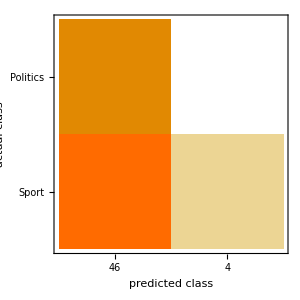
{0.48,-Graphics-}

```mathematica
catIdentifyMm/@{"Accuracy","ConfusionMatrixPlot"}
```

NaiveBayes without getBody

```mathematica
catIdentifyN =Classify[
Join[
Thread[politicsTraining-> "Politics"], 
Thread[sportTraining->"Sport"]],Method->"NaiveBayes"]
```

ClassifierFunction[…]

```mathematica
catIdentifyN[test]
```

{Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Sport,Politics,Politics,Politics,Politics,Politics,Politics,Sport,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Sport,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics}

```mathematica
catIdentifyNm= ClassifierMeasurements[catIdentifyN, Join[
Thread[polTestTexts-> "Politics"], 
Thread[sportTestTexts->"Sport"]
]]
```

ClassifierMeasurementsObject[…]

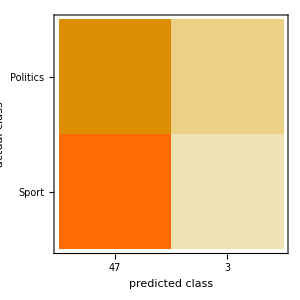
{0.38,-Graphics-}

```mathematica
catIdentifyNm/@{"Accuracy","ConfusionMatrixPlot"}
```

Markov+getBody

```mathematica
polTrainBody=getBody[politicsTraining];
```

```mathematica
sportTrainBody= getBody[sportTraining];
```

```mathematica
polTestBody=getBody[polTestTexts];
```

```mathematica
sportTestBody=getBody[sportTestTexts];
```

```mathematica
testgB=Join[polTestBody,sportTestBody];
```

```mathematica
catIdentifyMg =Classify[
Join[
Thread[polTrainBody-> "Politics"], 
Thread[sportTrainBody->"Sport"]]]
```

ClassifierFunction[…]

```mathematica
catIdentifyMg[testgB]
```

{Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Sport,Sport,Politics,Sport,Sport,Sport,Politics,Sport,Sport,Politics,Sport,Sport,Politics,Sport,Sport,Politics,Sport,Sport,Politics,Politics,Sport,Sport,Politics,Politics,Sport,Sport,Sport}

```mathematica
catIdentifyMgm= ClassifierMeasurements[catIdentifyMg, Join[
Thread[polTestBody-> "Politics"], 
Thread[sportTestBody->"Sport"]
]]
```

ClassifierMeasurementsObject[…]

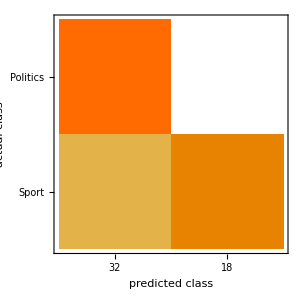
{0.76,-Graphics-}

```mathematica
catIdentifyMgm/@{"Accuracy","ConfusionMatrixPlot"}
```

NaiveBayes+getBody

```mathematica
catIdentifyNg =Classify[
Join[
Thread[polTrainBody-> "Politics"], 
Thread[sportTrainBody->"Sport"]],Method->"NaiveBayes"]
```

ClassifierFunction[…]

```mathematica
catIdentify[testgB]
```

{Sport,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Sport,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Politics,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport,Sport}

```mathematica
catIdentifyNgm= ClassifierMeasurements[catIdentifyNg, Join[
Thread[polTestBody-> "Politics"], 
Thread[sportTestBody->"Sport"]
]]
```

ClassifierMeasurementsObject[…]

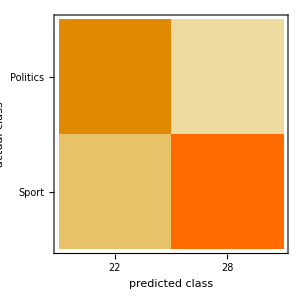
{0.8,-Graphics-}

```mathematica
catIdentifyNgm/@{"Accuracy","ConfusionMatrixPlot"}
```

## Creating the Form

```mathematica
CloudDeploy[FormPage["URL"->"URL",First[catIdentifyNg[getBody[{Import[#URL,"Plaintext"]}]]]&, AppearanceRules-><|"Title"->"Identifier of Articles' Categories", "Description"->"Insert the URL of the politics or sport Article's page and get the category name of the article"|>]]
```

CloudObject[]